## Checking Justin’s calculations

```mathematica
1(1-2M r/Σ)dv^2 - 2dv dr +4 a M r Sin[θ]^2/Σ dv dψ + 2a Sin[θ]^2dr dψ - Σ dθ^2-(a^2+r^2+2M r a^2/Σ Sin[θ]^2)Sin[θ]^2 dψ^2;
```

```mathematica
%/.{dv->dt+(r^2+a^2)/Δ dr, dψ->dϕ+a/Δ dr}
```

-2 dr (dt+(dr (a^2+r^2))/Δ)+(dt+(dr (a^2+r^2))/Δ)^2 (1-(2 M r)/Σ)-dθ^2 Σ+2 a dr (dϕ+(a dr)/Δ) Sin[θ]^2+(4 a M r (dϕ+(a dr)/Δ) (dt+(dr (a^2+r^2))/Δ) Sin[θ]^2)/Σ-(dϕ+(a dr)/Δ)^2 Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/Σ)

```mathematica
%//Expand
```

```mathematica
-a^2 dϕ^2 Sin[θ]^2-dϕ^2 r^2 Sin[θ]^2-(2 a^2 dϕ^2 M r Sin[θ]^4)/Σ
```

```mathematica
%//Simplify
```

1/(Δ^2 Σ)(-2 dr^2 M r^5-4 dr dt M r^3 Δ-2 dt^2 M r Δ^2+dr^2 r^4 Σ-2 dr^2 r^2 Δ Σ+2 dr dt r^2 Δ Σ-2 dr dt Δ^2 Σ+dt^2 Δ^2 Σ-dθ^2 Δ^2 Σ^2+a^4 dr^2 (-2 M r+Σ)-2 a^2 dr (2 dr M r^3+dt Δ (2 M r-Σ)+dr (-r^2+Δ) Σ)+(a dr+dϕ Δ) (4 a dt M r Δ+a^3 dr (4 M r-Σ)-a^2 dϕ Δ Σ-dϕ r^2 Δ Σ+a dr (4 M r^3-r^2 Σ+2 Δ Σ)) Sin[θ]^2-2 a^2 M r (a dr+dϕ Δ)^2 Sin[θ]^4)

```mathematica
{{1-(2 M r)/Σ,-1 +a^2/Δ+r^2/Δ-(2 a^2  M r)/(Δ Σ)-(2  M r^3)/(Δ Σ)+(2 a^2  M r Sin[θ]^2)/(Δ Σ),0,+(2 a  M r Sin[θ]^2)/Σ},{-1 +a^2/Δ+r^2/Δ-(2 a^2  M r)/(Δ Σ)-(2  M r^3)/(Δ Σ)+(2 a^2  M r Sin[θ]^2)/(Δ Σ),+a^4/Δ^2+(2 a^2  r^2)/Δ^2+r^4/Δ^2-(2 a^2)/Δ-(2  r^2)/Δ-(2 a^4 M r)/(Δ^2 Σ)-(4 a^2  M r^3)/(Δ^2 Σ)-(2  M r^5)/(Δ^2 Σ)-(a^4 Sin[θ]^2)/Δ^2-(a^2  r^2 Sin[θ]^2)/Δ^2+(2 a^2  Sin[θ]^2)/Δ+(4 a^4  M r Sin[θ]^2)/(Δ^2 Σ)+(4 a^2  M r^3 Sin[θ]^2)/(Δ^2 Σ)-(2 a^4  M r Sin[θ]^4)/(Δ^2 Σ),0,-(a^3  Sin[θ]^2)/Δ-(a  r^2 Sin[θ]^2)/Δ+(2 a^3 M r Sin[θ]^2)/(Δ Σ)+(2 a M r^3 Sin[θ]^2)/(Δ Σ)-(2 a^3 M r Sin[θ]^4)/(Δ Σ)+ a  Sin[θ]^2},{0,0,-Σ,0},{+(4 a  M r Sin[θ]^2)/Σ,-(a^3  Sin[θ]^2)/Δ-(a  r^2 Sin[θ]^2)/Δ+(2 a^3 M r Sin[θ]^2)/(Δ Σ)+(2 a M r^3 Sin[θ]^2)/(Δ Σ)-(2 a^3 M r Sin[θ]^4)/(Δ Σ)+ a  Sin[θ]^2,0,-a^2 dϕ^2 Sin[θ]^2-dϕ^2 r^2 Sin[θ]^2-(2 a^2 dϕ^2 M r Sin[θ]^4)/Σ}}//Simplify//MatrixForm
```

(1-(2 M r)/Σ | (-2 M r^3+r^2 Σ-Δ Σ+a^2 (-2 M r+Σ)+2 a^2 M r Sin[θ]^2)/(Δ Σ) | 0 | (2 a M r Sin[θ]^2)/Σ
(-2 M r^3+r^2 Σ-Δ Σ+a^2 (-2 M r+Σ)+2 a^2 M r Sin[θ]^2)/(Δ Σ) | -((a^2+2 r^2+a^2 Cos[2 θ]) (2 M r^3+a^2 (M r-Σ)-r^2 Σ+2 Δ Σ+a^2 M r Cos[2 θ]))/(2 Δ^2 Σ) | 0 | (a (2 M r^3+a^2 (M r-Σ)-r^2 Σ+Δ Σ+a^2 M r Cos[2 θ]) Sin[θ]^2)/(Δ Σ)
0 | 0 | -Σ | 0
(4 a M r Sin[θ]^2)/Σ | (a (2 M r^3+a^2 (M r-Σ)-r^2 Σ+Δ Σ+a^2 M r Cos[2 θ]) Sin[θ]^2)/(Δ Σ) | 0 | -(dϕ^2 Sin[θ]^2 ((a^2+r^2) Σ+2 a^2 M r Sin[θ]^2))/Σ)

```mathematica
((a^2+r^2) Σ+2 a^2 M r Sin[θ]^2)/.Σ->(r^2+a^3Sin[θ]^2)//Simplify
```

2 a^2 M r Sin[θ]^2+(a^2+r^2) (r^2+a^3 Sin[θ]^2)

```mathematica
{{1,(r^2+a^2)/Δ,0,0},{0,1,0,0},{0,0,1,0},{0,a/Δ,0,1}}
```

{{1,(a^2+r^2)/Δ,0,0},{0,1,0,0},{0,0,1,0},{0,a/Δ,0,1}}

```mathematica
Inverse[%]
```

{{1,-a^2/Δ-r^2/Δ,0,0},{0,1,0,0},{0,0,1,0},{0,-a/Δ,0,1}}

```mathematica
transf = {dt->dv + (-a^2/Δ-r^2/Δ)dr,dϕ->-a/Δ dr + dϕ}
```

{dt→dv+dr (-a^2/Δ-r^2/Δ),dϕ→dϕ-(a dr)/Δ}

```mathematica
(1-2Mr/Σ)dt^2+2(2M)
```

### eq. 20f

```mathematica
Assuming[{a>0,M>a},(M/2) (r^2-a^2)/((r^2+a^2)^2) - Sqrt[1-(a^2) / (M^2)]/(4 M (1+Sqrt[1-(a^2)/(M^2)]))/.{r->M+Sqrt[M^2-a^2]}]//Simplify
```

-(a^2+(-1+√(1-a^2/M^2)) M (M+√(-a^2+M^2)))/(4 (1+√(1-a^2/M^2)) M (M+√(-a^2+M^2))^2)

```mathematica
(a^2+(-1+√(1-a^2/M^2)) M (M+√(-a^2+M^2)))/(4 (1+√(1-a^2/M^2)) M (M+√(-a^2+M^2))^2)/.{a->0.6,M->1}
```

2.37959×10^-18

```mathematica
Assuming[{a>0,M>a},(M/2) (r^2-a^2)/((r^2+a^2)^2) /.{r->M+Sqrt[M^2-a^2]}]//Simplify
```

(-a^2+M (M+√(-a^2+M^2)))/(4 M (M+√(-a^2+M^2))^2)

```mathematica
Assuming[{a>0,M>a},(M^2+M Sqrt[M^2-a^2]-a^2)/(M+Sqrt[M^2-a^2] )]//Simplify
```

M-a^2/(M+√(-a^2+M^2))

### Eq. 65

Starting from eq.58 (removing prefactor)

```mathematica
eq = (2M^2 rp dM -J dJ)/Sqrt[M^4-J^2];
```

```mathematica
replace = dJ-> m ωr /(Abs[ω]^2)dM;
```

```mathematica
eq2 = eq/.{rp->M+Sqrt[M^2-a^2],replace}//Simplify
```

(2 dM M^2 (M+√(-a^2+M^2))-(dM J m ωr)/Abs[ω]^2)/(√(-J^2+M^4))

```mathematica
Clear[ΩH]
Solve[ΩH == a/(2 M rp)/.{rp->M+Sqrt[M^2-a^2]},a]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{a→(4 M^2 ΩH)/(1+4 M^2 ΩH^2)}}

```mathematica
eq2//.{J->a/M,a->(4 M^2 ΩH)/(1+4 M^2 ΩH^2)}//Simplify
```

(2 dM M^2 (M+√(M^2-(16 M^4 ΩH^2)/((1+4 M^2 ΩH^2)^2)))-(4 dM m M ΩH ωr)/((1+4 M^2 ΩH^2) Abs[ω]^2))/(√(M^4-(16 M^2 ΩH^2)/((1+4 M^2 ΩH^2)^2)))

```mathematica
%/.{ΩH-> (ωr-k)/m}
```

(2 dM M^2 (M+√(M^2-(16 M^4 (-k+ωr)^2)/(m^2 (1+(4 M^2 (-k+ωr)^2)/m^2)^2)))-(4 dM M ωr (-k+ωr))/((1+(4 M^2 (-k+ωr)^2)/m^2) Abs[ω]^2))/(√(M^4-(16 M^2 (-k+ωr)^2)/(m^2 (1+(4 M^2 (-k+ωr)^2)/m^2)^2)))

```mathematica
%//Simplify
```

(2 dM M (M (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))-(2 ωr (-k+ωr))/((1+(4 M^2 (k-ωr)^2)/m^2) Abs[ω]^2)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))

```mathematica
%/.Abs[ω]->ωr
```

(2 dM M (M (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))-(2 (-k+ωr))/((1+(4 M^2 (k-ωr)^2)/m^2) ωr)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))

```mathematica
%//Simplify
```

(2 dM M (M (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))-(2 (-k+ωr))/((1+(4 M^2 (k-ωr)^2)/m^2) ωr)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))

```mathematica
(2  M (M (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))-(2 (-k+ωr))/((1+(4 M^2 (k-ωr)^2)/m^2) ωr)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2))) - 2 M k(M+Sqrt[M^2-a^2])/(ωr Sqrt[M^4-J^2]) //.{J->a/M,a->(4 M^2 ΩH)/(1+4 M^2 ΩH^2),ΩH-> (ωr-k)/m}//Simplify
```

(2 M (M (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))-(k (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2))))/ωr-(2 (-k+ωr))/((1+(4 M^2 (k-ωr)^2)/m^2) ωr)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))

```mathematica
%/.{k->0.1,ωr->0.2,M->1,m->1}
```

2.40548×10^-16

```mathematica
Assuming[{M>0,ωr>0,m>0},(2  M (M (M+√(M^2-(16 m^2 M^4 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))-(2 ωr (-k+ωr))/((1+(4 M^2 (k-ωr)^2)/m^2) Abs[ω]^2)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))//Expand//Simplify]
```

(2 M (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))

```mathematica
TeXForm[%]
```

\frac{2 M^3 | \omega | ^2 \left(\left| m^2-4 M^2 (k-\text{$\omega $r})^2\right| +4 M^2 (k-\text{$\omega $r})^2+m^2\right)+4 m^2 M \text{$\omega $r} (k-\text{$\omega
   $r})}{| \omega | ^2 \left(4 M^2 (k-\text{$\omega $r})^2+m^2\right) \sqrt{M^4-\frac{16 m^2 M^2 (k-\text{$\omega $r})^2}{\left(4 M^2 (k-\text{$\omega
   $r})^2+m^2\right)^2}}}

```mathematica
Clear[dA]
```

```mathematica
Solve[dA == 8π (2 M (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))dM,dM]//Expand//Simplify
```

{{dM→(dA √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))}}

```mathematica
Solve[{dA == 8π (2 M (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))/(√(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))(m ωr /(Abs[ω]^2))^(-1)dJ},dJ]//Simplify
```

{{dJ→(dA m √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)) ωr)/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)) Abs[ω]^2)}}

```mathematica
daCalc = 1/M (dJ+a dM)/.{dJ->(dACalc m √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)) ωr)/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)) Abs[ω]^2),dM->(dACalc √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))}//Expand//Simplify
```

(dACalc √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)) (a+(m ωr)/Abs[ω]^2))/(16 M^2 π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))

```mathematica
dMCalc = (dACalc √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))
```

(dACalc √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)))

```mathematica
TeXForm[(dA m √(M^4-(16 m^2 M^2 (k-ωr)^2)/((m^2+4 M^2 (k-ωr)^2)^2)) ωr)/(16 M π (M (M+√(((m^2 M-4 M^3 (k-ωr)^2)^2)/((m^2+4 M^2 (k-ωr)^2)^2)))+(2 m^2 (k-ωr) ωr)/((m^2+4 M^2 (k-ωr)^2) Abs[ω]^2)) Abs[ω]^2)]
```

\frac{\text{dA} m \text{$\omega $r} \sqrt{M^4-\frac{16 m^2 M^2 (k-\text{$\omega $r})^2}{\left(4 M^2 (k-\text{$\omega $r})^2+m^2\right)^2}}}{16 \pi  M | \omega | ^2
   \left(\frac{2 m^2 \text{$\omega $r} (k-\text{$\omega $r})}{| \omega | ^2 \left(4 M^2 (k-\text{$\omega $r})^2+m^2\right)}+M \left(\sqrt{\frac{\left(m^2 M-4 M^3
   (k-\text{$\omega $r})^2\right)^2}{\left(4 M^2 (k-\text{$\omega $r})^2+m^2\right)^2}}+M\right)\right)}

## Calculating Change in M, a

Checking σ converges

```mathematica
σ = Exp[-I ω v]/(2ϵ-I ω v)//.{ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],ω->0.49404-I*0.08376}
```

ⅇ^((-0.08376-0.49404 ⅈ) v)/(0.222222-(0.08376+0.49404 ⅈ) v)

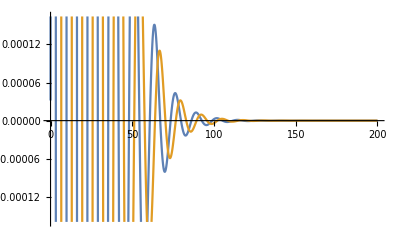

```mathematica
Plot[{Im[Exp[-I ω v]/(2ϵ-I ω v)//.{ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],ω->0.49404-I*0.08376}],Re[Exp[-I ω v]/(2ϵ-I ω v)//.{ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],ω->0.49404-I*0.08376}]},{v,0,200}]
```

ρ(2) goes like |σ(1)|^2

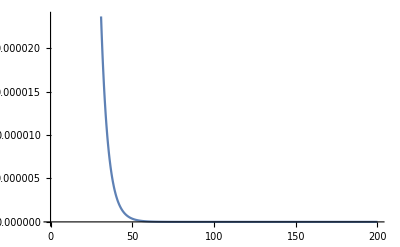

```mathematica
Plot[Abs[σ/.v->vp]^2,{vp,0,200}]
```

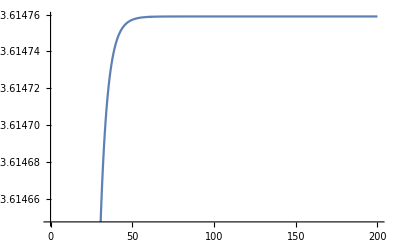

```mathematica
Plot[NIntegrate[Abs[σ/.v->vp]^2,{vp,0,vpp}],{vpp,0,200}]
```

```mathematica
Exp[2ϵ (vpp-v)]Abs[σ]^2
```

ⅇ^(2 (-v+vpp) ϵ+2 Re[(-0.08376-0.49404 ⅈ) v])/Abs[0.222222-(0.08376+0.49404 ⅈ) v]^2

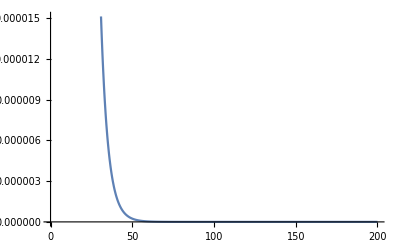

```mathematica
Plot[Exp[2ϵ (vpp-v)]Abs[σ]^2//.{ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,v->vpp+1},{vpp,0,200}]
```

```mathematica
Plot[Integrate[Exp[2ϵ (vpp-v)]Abs[σ]^2,{v,vp,∞}]/.vp->vpp,{vpp,0,200}]
```

$Aborted

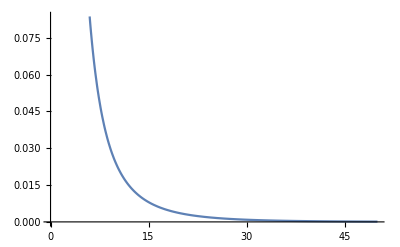

```mathematica
Plot[Exp[2ϵ(vp-vpp)-2 Iω vpp]/(Abs[2 ϵ+Iω vpp]^2+Abs[Rω vpp]^2)//.{vp->0.1,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],Iω->-0.08376,Rω->0.49404},{vpp,0,50}]
```

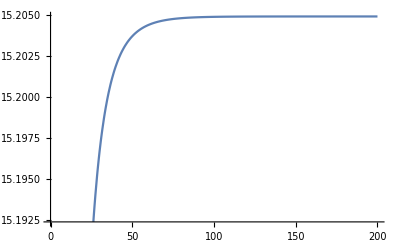

```mathematica
Plot[NIntegrate[Exp[2ϵ(vp-vpp)-2 Iω vpp]/(Abs[2 ϵ+Iω vpp]^2+Abs[Rω vpp]^2)//.{vp->0.1,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],Iω->-0.08376,Rω->0.49404},{vpp,0,vppp}],{vppp,0,200}]
```

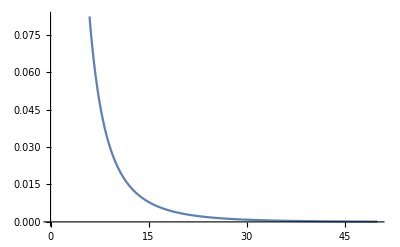

```mathematica
Plot[Exp[2ϵ(vp-vpp)-2 Iω vpp]/(4 Abs[ϵ]^2+Abs[ω vpp]^2)//.{vp->0.1,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],Iω->-0.08376},{vpp,0,50}]
```

```mathematica
Clear[ϵ,Iω,ω]
```

#### Checking lim v-> ∞ of ρ

```mathematica
Series[1/(4 Rω ϵ)ⅈ ⅇ^(-(2 (Iω^2 vpint+ⅈ Rω vp ϵ+Iω (-vp+vpint) ϵ))/(Iω-ⅈ Rω)) (ⅇ^((2 (Iω+ϵ) (Iω vpint+2 ϵ))/(Iω-ⅈ Rω)) Gamma[0,(2 (Iω+ϵ) (Iω vpint-ⅈ Rω vpint+2 ϵ))/(Iω-ⅈ Rω)]-ⅇ^((2 (Iω+ϵ) (Iω^2 vpint+ⅈ Iω Rω vpint+2 Iω ϵ-2 ⅈ Rω ϵ))/(Iω^2+Rω^2)) Gamma[0,(2 (Iω+ϵ) (Iω vpint+ⅈ Rω vpint+2 ϵ))/(Iω+ⅈ Rω)]+ⅇ^((2 (Iω+ϵ) (Iω vpint+2 ϵ))/(Iω-ⅈ Rω)) (-Log[Iω+ϵ]+Log[(Iω-ⅈ Rω)/(Iω vpint-ⅈ Rω vpint+2 ϵ)]+Log[((Iω+ϵ) (Iω vpint-ⅈ Rω vpint+2 ϵ))/(Iω-ⅈ Rω)]))/.vpint->vp,vp->∞]
```

ⅇ^(-2 Iω vp+O[1/vp]^2) (-ⅈ/(8 Rω ϵ (Iω+ϵ) vp)+O[1/vp]^2)+ⅇ^(-2 Iω vp+O[1/vp]^2) (ⅈ/(8 Rω ϵ (Iω+ϵ) vp)+O[1/vp]^2)+ⅇ^(2 ϵ vp+O[1/vp]^0) (-(ⅈ (Log[vp]+Log[Iω+ϵ]-Log[vp (Iω+ϵ)]))/(4 Rω ϵ)+O[1/vp]^2)

```mathematica
ⅇ^(-2 Iω vp+O[1/vp]^2) (-ⅈ/(8 Rω ϵ (Iω+ϵ) vp)+O[1/vp]^2)+ⅇ^(-2 Iω vp+O[1/vp]^2) (ⅈ/(8 Rω ϵ (Iω+ϵ) vp)+O[1/vp]^2)+ⅇ^(2 ϵ vp+O[1/vp]^0) (-(ⅈ (Log[vp]+Log[Iω+ϵ]-Log[vp (Iω+ϵ)]))/(4 Rω ϵ)+O[1/vp]^2)//.{O[1/vp]^2->0,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],Rω->0.49404,Iω->−0.08376}
```

ⅇ^(0.16752 vp+O[1/vp]^2) (-(0.+83.256 ⅈ)/vp+O[1/vp]^2)+ⅇ^(0.16752 vp+O[1/vp]^2) ((0.+83.256 ⅈ)/vp+O[1/vp]^2)

So there is some divergent part but it cancels out numerically

So taking the expansion of ρ at v-> ∞ gives zero. No analytic divergence at ∞.

#### Now calculating explicitly and looking at potential parts that are blowing up

```mathematica
Assuming[{ϵ>0,Iω<0,Rω>0,vp>0,vpp>vp},Integrate[Exp[2ϵ(vp-vpp)+2 Iω vpp]/(Abs[2 ϵ+Iω ]^2+Abs[Rω ]^2),{vpp,vpint,∞}]]/.vpint->vp
```

ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))

```mathematica
toPlot[vp_]:=ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],Rω->0.49404,Iω->−0.08376};
```

Diverging part of ρ

```mathematica
Re[(0.6671677880533725-3.935142956183001 ⅈ) (0.+(0.0070157376+0.054893333333333336 ⅈ))]
```

0.220694

Converging part

```mathematica
(ⅇ^((2 (Iω+ϵ) (Iω vpint+2 ϵ))/(Iω-ⅈ Rω)) Gamma[0,(2 (Iω+ϵ) (Iω vpint-ⅈ Rω vpint+2 ϵ))/(Iω-ⅈ Rω)]-ⅇ^((2 (Iω+ϵ) (Iω^2 vpint+ⅈ Iω Rω vpint+2 Iω ϵ-2 ⅈ Rω ϵ))/(Iω^2+Rω^2)) Gamma[0,(2 (Iω+ϵ) (Iω vpint+ⅈ Rω vpint+2 ϵ))/(Iω+ⅈ Rω)]+ⅇ^((2 (Iω+ϵ) (Iω vpint+2 ϵ))/(Iω-ⅈ Rω)) (-Log[Iω+ϵ]+Log[(Iω-ⅈ Rω)/(Iω vpint-ⅈ Rω vpint+2 ϵ)]+Log[((Iω+ϵ) (Iω vpint-ⅈ Rω vpint+2 ϵ))/(Iω-ⅈ Rω)]))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Abs[ω]->Sqrt[0.49404^2+0.08376^2],Rω->0.49404,Iω->−0.08376}
```

ⅇ^((-0.0182478+0.107631 ⅈ) (0.222222-0.08376 vp)) Gamma[0,(-0.0182478+0.107631 ⅈ) (0.222222-(0.08376+0.49404 ⅈ) vp)]-ⅇ^(0.217858 ((-0.0186133-0.109787 ⅈ)+(0.00701574-0.0413808 ⅈ) vp)) Gamma[0,(-0.0182478-0.107631 ⅈ) (0.222222-(0.08376-0.49404 ⅈ) vp)]+ⅇ^((-0.0182478+0.107631 ⅈ) (0.222222-0.08376 vp)) (3.599+Log[-(0.08376+0.49404 ⅈ)/(0.222222-(0.08376+0.49404 ⅈ) vp)]+Log[(-0.00912389+0.0538153 ⅈ) (0.222222-(0.08376+0.49404 ⅈ) vp)])

```mathematica
Series[ⅇ^((-0.018247780300802024+0.10763053223266754 ⅈ) (0.22222222222222224-0.08376 vp)) Gamma[0,(-0.018247780300802024+0.10763053223266754 ⅈ) (0.22222222222222224-(0.08376+0.49404 ⅈ) vp)]-ⅇ^(0.2178579310028895 ((-0.018613333333333336-0.10978666666666667 ⅈ)+(0.0070157376-0.0413807904 ⅈ) vp)) Gamma[0,(-0.018247780300802024-0.10763053223266754 ⅈ) (0.22222222222222224-(0.08376-0.49404 ⅈ) vp)]+ⅇ^((-0.018247780300802024+0.10763053223266754 ⅈ) (0.22222222222222224-0.08376 vp)) (3.5989981253045698+Log[-(0.08376+0.49404 ⅈ)/(0.22222222222222224-(0.08376+0.49404 ⅈ) vp)]+Log[(-0.009123890150401012+0.05381526611633377 ⅈ) (0.22222222222222224-(0.08376+0.49404 ⅈ) vp)]),vp->∞]
```

ⅇ^(-(0.0531738+0.00901513 ⅈ) vp+O[1/vp]^0) (-(18.2808-4.44089×10^-16 ⅈ)/vp+O[1/vp]^2)+ⅇ^(-(0.0531738+0.00901513 ⅈ) vp+O[1/vp]^2) ((18.2808+4.44089×10^-16 ⅈ)/vp+O[1/vp]^2)+ⅇ^((0.00152843-0.00901513 ⅈ) vp+O[1/vp]^0) (((0.-3.17121×10^-17 ⅈ)+Log[(1.+0. ⅈ)/vp]+Log[vp])+O[1/vp]^2)

Now looking at numerical issues

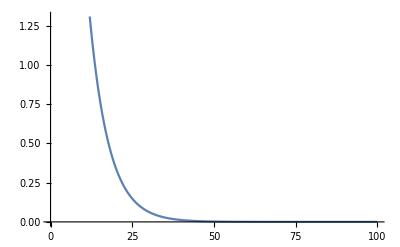

```mathematica
Plot[{Re[toPlot[vp]]},{vp,0,100}]
```

#### Comparing to Poisson (pure mode dA/dv ~ 5.22)

```mathematica
Clear[σ]
```

```mathematica
DSolve[D[ρ[v],v]==2ϵ ρ[v] + σ ,ρ,v]
```

{{ρ→Function[{v},-σ/(2 ϵ)+ⅇ^(2 v ϵ) C[1]]}}

```mathematica
Integrate[- Exp[2ϵ(v-vp) ]σ,{vp,vpint,∞}]/.vpint->v//Simplify
```

ConditionalExpression[-σ/(2 ϵ), Re[ϵ]>0]

```mathematica
toNum = {MIn->1,aIn->0.6,Rω->0.49404,Iω->0};
```

```mathematica
ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{Iω->0,vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),aIn->a,MIn->M}//Simplify
```

(2 M (M+√(-a^2+M^2)))/(√(-a^2+M^2) ((-a^2+M^2)/(4 M^2 (M+√(-a^2+M^2))^2)+Rω^2))

```mathematica
PoissonAdot = (2/κ)(rp^2+a^2)/(κ^2+k^2) ;
```

```mathematica
PoissontoHere = {κ -> (rp-M)/(rp^2+a^2),rp->M+Sqrt[M^2-a^2],k->Rω};
PoissontoHere2 = {κ -> 2ϵ,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),aIn->a,MIn->M,rp->M+Sqrt[M^2-a^2],k->Rω};
```

Find both conditions are equivalent.

```mathematica
PoissonAdot//.PoissontoHere2//Simplify
```

(32 M^4 (M+√(-a^2+M^2))^4)/(√(-a^2+M^2) (-a^2 (1+4 M^2 Rω^2)+M^2 (1+8 M^2 Rω^2+8 M √(-a^2+M^2) Rω^2)))

```mathematica
(2 M (M+√(-a^2+M^2)))/(√(-a^2+M^2) ((-a^2+M^2)/(4 M^2 (M+√(-a^2+M^2))^2)+Rω^2))/((32 M^4 (M+√(-a^2+M^2))^4)/(√(-a^2+M^2) (-a^2 (1+4 M^2 Rω^2)+M^2 (1+8 M^2 Rω^2+8 M √(-a^2+M^2) Rω^2))))//Simplify
```

1/(4 M^2+4 M √(-a^2+M^2))

So factor of 4Mr+ difference.. -> Dimensionally different

```mathematica
(2)(rp^2+a^2)//.PoissontoHere//Simplify
```

4 M (M+√(-a^2+M^2))

Now want to do for our induced metric

```mathematica
Sqrt[((rp^2+a^2Cos[θ]^2)(a^2+rp^2)+2M rp a^2Sin[θ]^2)Sin[θ]^2]//Simplify
```

√((a^2+rp^2) (rp^2+a^2 Cos[θ]^2) Sin[θ]^2+2 a^2 M rp Sin[θ]^4)

```mathematica
%/.{rp->M+Sqrt[M^2-a^2]}
```

√((a^2+(M+√(-a^2+M^2))^2) ((M+√(-a^2+M^2))^2+a^2 Cos[θ]^2) Sin[θ]^2+2 a^2 M (M+√(-a^2+M^2)) Sin[θ]^4)

```mathematica
Assuming[{M>0,M>a>0,θ>0},Simplify[√((a^2+(M+√(-a^2+M^2))^2) ((M+√(-a^2+M^2))^2+a^2 Cos[θ]^2) Sin[θ]^2+2 a^2 M (M+√(-a^2+M^2)) Sin[θ]^4)]]
```

2 M √(-a^2+2 M (M+√(-a^2+M^2))) Abs[Sin[θ]]

```mathematica
TeXForm[%]
```

2 M \sqrt{2 M \left(\sqrt{M^2-a^2}+M\right)-a^2} | \sin (\theta )|

```mathematica
Integrate[ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2)),{vp,v1,v2}]
```

(-ⅇ^(2 Iω v1)+ⅇ^(2 Iω v2))/(4 Iω (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))

```mathematica
TeXForm[%]
```

\frac{e^{2 \text{I$\omega $} \text{v2}}-e^{2 \text{I$\omega $} \text{v1}}}{4 \text{I$\omega $} (\epsilon -\text{I$\omega $}) \left((\text{I$\omega $}+2 \epsilon
   )^2+\text{R$\omega $}^2\right)}

#### Now evolving to solve equations

```mathematica
Assuming[{ϵ>0,Iω<0,vp>0,vpp>vp},Integrate[Exp[2ϵ(vp-vpp)-2 Iω vpp]/(4 Abs[ϵ]^2+Abs[ω vpp]^2),{vpp,vpint,∞}]]
```

ConditionalExpression[-(ⅈ ⅇ^(2 ϵ (vp-(2 ⅈ (Iω+ϵ))/Abs[ω])) (Gamma[0,2 (Iω+ϵ) (vpint-(2 ⅈ ϵ)/Abs[ω])]-ⅇ^((8 ⅈ ϵ (Iω+ϵ))/Abs[ω]) Gamma[0,2 (Iω+ϵ) (vpint+(2 ⅈ ϵ)/Abs[ω])]))/(4 ϵ Abs[ω]), ]

```mathematica
toPlot1[vp_]:= ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.0,Rω->0.37367,Iω->−0.08896};
toPlot2[vp_]:=ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.5,Rω->0.464123,Iω->−0.08564};
toPlot3[vp_]:=ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Rω->0.49404,Iω->−0.08376};
toPlot4[vp_]:=ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.7,Rω->0.5326,Iω->−0.0807928};
toPlot5[vp_]:=ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.9,Rω->0.6717142,Iω->−0.0648692};
toPlot6[vp_]:=ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.99,Rω->0.8708926,Iω->−0.0293904};
```

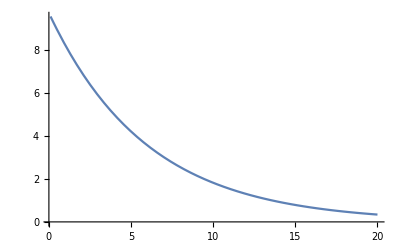

```mathematica
Plot[ⅇ^(2 Iω vp)/(2 (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))//.{vpint->vp,ϵ -> Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2])),MIn->1,aIn->0.6,Rω->0.49404,Iω->-0.08376},{vp,0.1,20}]
```

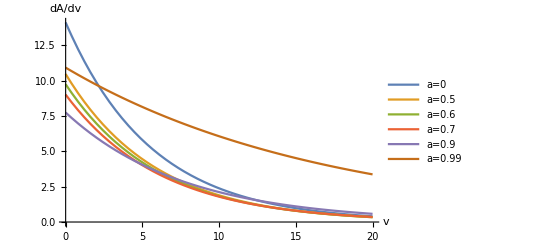

```mathematica
Plot[{toPlot1[v2],toPlot2[v2],toPlot3[v2],toPlot4[v2],toPlot5[v2],toPlot6[v2]},{v2,0,20},PlotLegends->{"a=0 ","a=0.5","a=0.6","a=0.7","a=0.9","a=0.99"},AxesLabel->{"v","dA/dv"}]
```

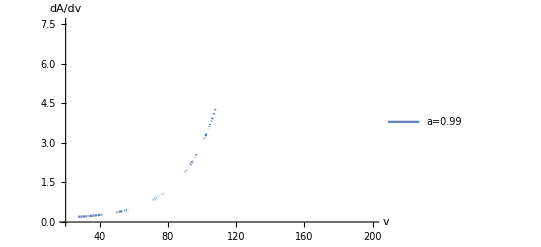

```mathematica
Plot[{toPlot6[v2]},{v2,20,200},PlotLegends->{"a=0.99"},AxesLabel->{"v","dA/dv"}]
```

Looks like the exponential dominates for late time



Choosing M = 1
For a= 0.6M -- M ω22 = 0.49404 − 0.08376i

```mathematica
ω = Abs[0.49404];
Iω = −0.08376;
ϵ = Sqrt[1-0.6^2]/(4(1+Sqrt[1-0.6^2]));
m = 2;
ao = 0.6;
Mo = 1;
k = ω-m (ao/(2(1+Sqrt[1-ao^2]))) ;
```

```mathematica
ΔA = 4π Amp^2NIntegrate[toint,{vp,0,1}]
```

89.3497 Amp^2

```mathematica
ΔM = Sqrt[Mo^2 - ao^2]/(16 π Mo) (ω / k )ΔA
```

4.37161 Amp^2

```mathematica
Δa = Sqrt[Mo^2 - ao^2]/(16 π Mo) (m-ao ω) /( Mo k )ΔA
```

15.0744 Amp^2

```mathematica
ω(Mo+ΔM) - ω Mo//Simplify
```

0.+2.15975 Amp^2

?? Cubic in amplitude effect? Project this using
<ψold | ψnew>		-> 	get another factor of amp?

Choosing Mo = 1 units and calculating for general example

```mathematica
Δ[ω_,Iω_,ao_,m_,v1_,v2_,Amp_]:=
Module[{ΔA,ΔM,Δa,k,ϵ,integrated},
ϵ = Sqrt[1-ao^2]/(4(1+Sqrt[1-ao^2]));
k = ω-m (ao/(2(1+Sqrt[1-ao^2]))) ;
integrated = 1/(8 ϵ^2 ω)ⅈ ⅇ^(-(4 ⅈ Iω ϵ)/ω) (ExpIntegralEi[Iω (-2 v1+(4 ⅈ ϵ)/ω)]-ExpIntegralEi[Iω (-2 v2+(4 ⅈ ϵ)/ω)]+ⅇ^((8 ⅈ Iω ϵ)/ω) (-ExpIntegralEi[-(2 Iω (2 ⅈ ϵ+v1 ω))/ω]+ExpIntegralEi[-(2 Iω (2 ⅈ ϵ+v2 ω))/ω]-ⅇ^(2 ϵ (v1+(2 ⅈ ϵ)/ω)) Gamma[0,2 (Iω+ϵ) (v1+(2 ⅈ ϵ)/ω)]+ⅇ^(2 ϵ (v2+(2 ⅈ ϵ)/ω)) Gamma[0,2 (Iω+ϵ) (v2+(2 ⅈ ϵ)/ω)])+ⅇ^(2 ϵ (v1-(2 ⅈ ϵ)/ω)) Gamma[0,(2 (Iω+ϵ) (-2 ⅈ ϵ+v1 ω))/ω]-ⅇ^(2 ϵ (v2-(2 ⅈ ϵ)/ω)) Gamma[0,(2 (Iω+ϵ) (-2 ⅈ ϵ+v2 ω))/ω]);
ΔA =  4π Amp^2 integrated;
ΔM = Sqrt[1 - ao^2]/(16 π ) (ω / k )ΔA;
Δa = Sqrt[1 - ao^2]/(16 π ) (m-ao ω) /( Mo k )ΔA;
Δa
]
```

```mathematica
Δ[0.464123,−0.08564,0.5,0,2,0,1,1]
```

```mathematica
Δ[0.464123,−0.08564,0.5,2,0,1,1]
```

{3.94485+2.13327×10^-16 ⅈ,15.0268+8.12604×10^-16 ⅈ}

```mathematica
toPlot1[v2_]:=Δ[0.37367,−0.08896,0,2,0,v2,1]
toPlot2[v2_]:=Δ[0.464123,−0.08564,0.5,2,0,v2,1]
toPlot3[v2_]:=Δ[0.49404,−0.08376,0.6,2,0,v2,1]
toPlot4[v2_]:=Δ[0.5326,−0.0807928,0.7,2,0,v2,1]
toPlot5[v2_]:=Δ[0.6717142,−0.0648692,0.9,2,0,v2,1]
toPlot6[v2_]:=Δ[0.8708926,−0.0293904,0.99,2,0,v2,1]
```

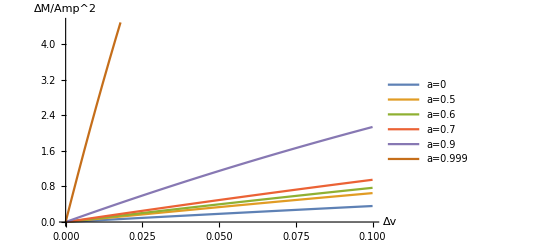

```mathematica
Plot[{toPlot1[v2],toPlot2[v2],toPlot3[v2],toPlot4[v2],toPlot5[v2],toPlot6[v2]},{v2,0,0.1},PlotLegends->{"a=0 ","a=0.5","a=0.6","a=0.7","a=0.9","a=0.999"},AxesLabel->{"Δv","ΔM/Amp^2"}]
```

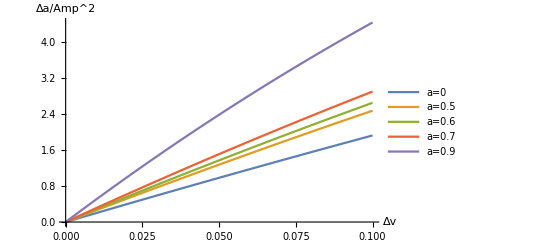

```mathematica
Plot[{toPlot1[v2],toPlot2[v2],toPlot3[v2],toPlot4[v2],toPlot5[v2]},{v2,0,0.1},PlotLegends->{"a=0 ","a=0.5","a=0.6","a=0.7","a=0.9"},AxesLabel->{"Δv","Δa/Amp^2"}]
```

Obviously this is bad -- should have a<1
-> need to solve continuously instead of for constant ϵ

### Now for new eq.s

```mathematica
evolve[Δv_,dv_,ωrIn_,ωi_,ao_,Mo_,mIn_,Amp_]:=
Module[{MIn,dM,aIn,da,dA,ϵ,v,vlast,kIn,integrated,Aω,v1,v2,Points,Mlast,alast},
Aω = Sqrt[ωrIn^2+ωi^2];
v1 = 0;
v2 = Δv;
Points={};
MIn = Mo;
aIn = ao;
For[v=0,v<Δv,v=vlast+dv,
ϵ = Sqrt[MIn^2-aIn^2]/(4MIn(MIn+Sqrt[MIn^2-aIn^2]));
kIn = ωrIn-mIn (aIn/(2(1+Sqrt[1-aIn^2]))) ;
v1 = vlast;
v2 = vlast+dv;
(*integrated = 1/(8 ϵ^2 Aω)ⅈ ⅇ^(-(4 ⅈ ωi ϵ)/Aω) (ExpIntegralEi[ωi (-2 v1+(4 ⅈ ϵ)/Aω)]-ExpIntegralEi[ωi (-2 v2+(4 ⅈ ϵ)/Aω)]+ⅇ^((8 ⅈ ωi ϵ)/Aω) (-ExpIntegralEi[-(2 ωi (2 ⅈ ϵ+v1 Aω))/Aω]+ExpIntegralEi[-(2 ωi (2 ⅈ ϵ+v2 Aω))/Aω]-ⅇ^(2 ϵ (v1+(2 ⅈ ϵ)/Aω)) Gamma[0,2 (ωi+ϵ) (v1+(2 ⅈ ϵ)/Aω)]+ⅇ^(2 ϵ (v2+(2 ⅈ ϵ)/Aω)) Gamma[0,2 (ωi+ϵ) (v2+(2 ⅈ ϵ)/Aω)])+ⅇ^(2 ϵ (v1-(2 ⅈ ϵ)/Aω)) Gamma[0,(2 (ωi+ϵ) (-2 ⅈ ϵ+v1 Aω))/Aω]-ⅇ^(2 ϵ (v2-(2 ⅈ ϵ)/Aω)) Gamma[0,(2 (ωi+ϵ) (-2 ⅈ ϵ+v2 Aω))/Aω]);*)
integrated =  (2 MIn √(-aIn^2+2 MIn (MIn+√(-aIn^2+MIn^2)))ⅇ^(2 ωi v))/(2 (-ωi+ϵ) (ωrIn^2+(ωi+2 ϵ)^2));
(*integrated = ⅇ^(2 ωi v);*)
dA =  4π Amp^2 integrated * dv;
dM = dMCalc /.{dACalc->dA,m->mIn,M->MIn,a->aIn,ωr->ωrIn,k->kIn,Abs[ω]->Aω};
da = daCalc /.{dACalc->dA,m->mIn,M->MIn,a->aIn,ωr->ωrIn,k->kIn,Abs[ω]->Aω};
vlast = v;
Mlast = MIn;
alast = aIn;
MIn = Mlast + dM;
aIn = alast +da;
Points=Append[Points,dA];
]
Points
]
```

Checking dA behaviour - should go like integrated * dv

Integrated:

Looking at fluxes:

For a= 0.6M -- M ω22 = 0.49404 − 0.08376i

```mathematica
test1 = evolve[10,0.0001,0.49404,-0.08376,0.6,1,2,0.009];
```

```mathematica
test2 = evolve[10,0.0001,0.6717142,−0.06486920,0.9,1,2,0.01];
```

```mathematica
test3 = evolve[10,0.0001,0.8708926,−0.0293904,0.99,1,2,0.01];
```

```mathematica
toplot1 = Re[test1/.Null ->(1)];
(*Part[Transpose[test1],1]/.Null ->(1)*)
toplot2 = Re[test2/.Null ->(1)];
toplot3 =Re[ test3/.Null ->(1)];
```

ΔA(v)

```mathematica
ListPlot[{Log[toplot1],Log[toplot2],Log[toplot3]},PlotLegends->{"a=0.6","a=0.9","a=0.99"}]
```

-Graphics-

```mathematica
Part[Transpose[test1],2]/.Null ->(1);
```

M(v)

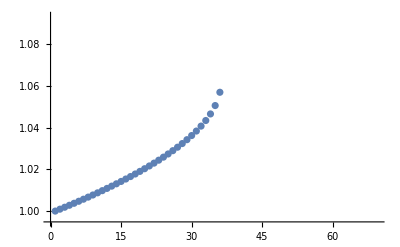

```mathematica
ListPlot[%]
```

a(v)

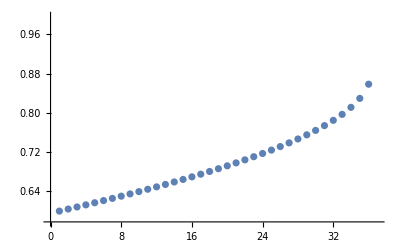

```mathematica
ListPlot[%]
```

```mathematica
test = evolve[10,0.0001,0.49404,-0.08376,0.6,1,2,0.01];
```

Plotting dA

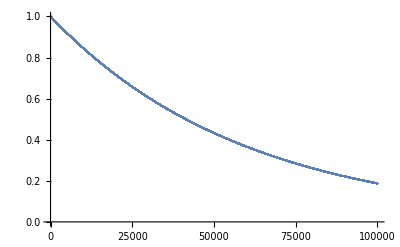

```mathematica
ListPlot[test1/.Null->(1)]
```

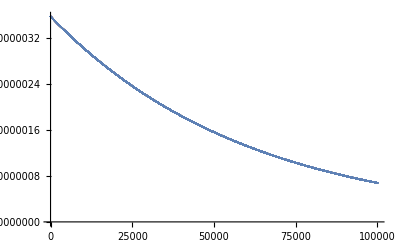

```mathematica
ListPlot[test1/.Null->(1)]
```

#### Linear level Calculation

* Initial Area = 26

Amp should go like what? Taking results from QNM ID code -- Λ == Econst

```mathematica
C2 = (Q^2+4a ω m - 4 a^2 ω^2)((Q-2)^2+36a ω m - 36 a^2 ω^2 ) +(2Q-1)(96a^2 ω^2 - 48a ω m) + 144 ω^2(M-a^2);
C1 = Abs[Sqrt[C2 //.{M->1,a->0.7,ω->0.5325999583183444-0.0807929627407481I,m->2,Q->(Econst + a^2 ω^2-2a ω m),Econst->-1.096839560138186+0.18315630111411232*I}]]
Dminus2 = 0.29;
```

22.706

```mathematica
AmpSub =Integrate[Rω^2 C1^-1 Dminus2 (M+Sqrt[M^2-a^2] -I a Cos[θ])^4//.{M->1,a->0.7,Rω->0.5325999583183444},{θ,0,π}]/π
```

0.0159564-4.22341×10^-15 ⅈ

```mathematica
ΔA =4π Amp^2 (-ⅇ^(2 Iω v1)+ⅇ^(2 Iω v2))/(4 Iω (-Iω+ϵ) (Rω^2+(Iω+2 ϵ)^2))2 M √(-a^2+2 M (M+√(-a^2+M^2)))//.{vpint->vp,ϵ -> Sqrt[M^2-a^2]/(4M(M+Sqrt[M^2-a^2])),M->1,a->0.7,Rω->0.5325999583183444,Iω->−0.0807929627407481,Amp->AmpSub,v1->0,v2->∞}
```

0.611877-3.23909×10^-13 ⅈ

```mathematica
0.6118774824186812/26
```

0.0235337

Verified that A goes like M^2 for Amp ~ 1/M^2

```mathematica
ΔM = dMCalc //.{dACalc->ΔA,m->2,M->1,a->0.7,ωr->0.5325999583183444,k->ωr-m (a/(2(1+Sqrt[1-a^2]))),Abs[ω]->Sqrt[0.5325999583183444^2+0.0807929627407481^2]}
Δa = daCalc //.{dACalc->ΔA,m->2,M->1,a->0.7,ωr->0.5325999583183444,k->ωr-m (a/(2(1+Sqrt[1-a^2]))),Abs[ω]->Sqrt[0.5325999583183444^2+0.0807929627407481^2]}
```

0.020245-1.07171×10^-14 ⅈ

0.0884848-4.68411×10^-14 ⅈ

```mathematica
0.088/0.7
```

0.125714

Want to check R_(-2) (r+) = R_(2) (r+) -- TRUE

```mathematica
R = Hypergeometric2F1[-2 I ω +s+1/2 +I δ,-2 I ω +s +1/2 - I δ,1+s+I κ, 0]
```

1

Want to calculate E for -2S22 spin spherical harmonic (Ignore since E is Λ and should be spheroidal not spherical)

```mathematica
Y[s_,l_,m_,th_,ph_]:=(-1)^m*Simplify[Sqrt[((l+m)!*(l-m)!*(2*l+1))/((l+s)!*(l-s)!*4*Pi)]*Sin[th/2]^(2*l)*Sum[Binomial[l-s,r]*Binomial[l+s,r+s-m]*(-1)^(l-r-s)*E^(I*m*ph)*Cot[th/2]^(2*r+s-m),{r,0,l-s}],Assumptions->{Element[ph,Reals],Element[th,Reals]}];
```

So from eq. 2.7 in https://articles.adsabs.harvard.edu/pdf/1974ApJ...193..443T

```mathematica
eqE = 1/(Sin[θ]) D[(Sin[θ]D[Y[2,2,2,θ,ϕ],θ]),θ] + (a^2 ω^2 Cos[θ]^2 - 2^2 /(Sin[θ]^2)-2 a ω 2 Cos[θ] - (2 *2*2 Cos[θ])/(Sin[θ]^2)-2^2 Cot[θ] +Econst - 2^2)Y[2,2,2,θ,ϕ]
```

1/2 ⅇ^(2 ⅈ ϕ) √(5/π) (-4+Econst-4 a ω Cos[θ]+a^2 ω^2 Cos[θ]^2-4 Cot[θ]-8 Cot[θ] Csc[θ]-4 Csc[θ]^2) Sin[θ/2]^4+Csc[θ] (ⅇ^(2 ⅈ ϕ) √(5/π) Cos[θ/2] Cos[θ] Sin[θ/2]^3+3/2 ⅇ^(2 ⅈ ϕ) √(5/π) Cos[θ/2]^2 Sin[θ/2]^2 Sin[θ]-1/2 ⅇ^(2 ⅈ ϕ) √(5/π) Sin[θ/2]^4 Sin[θ])

```mathematica
Solve[eqE==0,Econst]
```

{{Econst→5+4 a ω Cos[θ]-a^2 ω^2 Cos[θ]^2-3 Cot[θ/2]^2+4 Cot[θ]-2 Cot[θ/2] Cot[θ]+8 Cot[θ] Csc[θ]+4 Csc[θ]^2}}

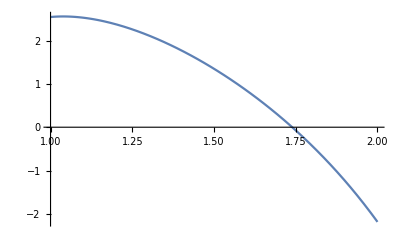

```mathematica
Plot[4 a ω Cos[θ]-a^2 ω^2 Cos[θ]^2-3 Cot[θ/2]^2+4 Cot[θ]-2 Cot[θ/2] Cot[θ]+8 Cot[θ] Csc[θ]+4 Csc[θ]^2/.{ϕ->0,θ->θp,a->0.6,ω->Sqrt[0.49404^2+0.08376^2]},{θp,1,2}]
```